```mathematica
(* Analytic calculation of one-loop energy correction for lower M cases. *)
<<"/users/gaolichen/gitroot/stringbit/mathematica/sbmatrices.m";
<<"/users/gaolichen/gitroot/stringbit/mathematica/sbgrassmann.m";
```

```mathematica
(* verify the 3-bit ground energy state*)
tmppsi=Psi2Theta[3,{}];
OutputEigenFunction[%]
tmp1=-tmppsi[[1]]
tmp2=tmppsi[[4]]*3
tmpv1={tmp1 * (-6)+tmp2*(-2I), tmp1*6*I+tmp2*6};
Simplify[tmpv1[[1]]/tmpv1[[2]]];
Simplify[tmp1/tmp2];
Simplify[%-%%]
Simplify[tmpv1[[1]]/tmp1]

FullSimplify[{tmp1,tmp2}.{-6I,2}];
FullSimplify[{tmp1,tmp2}.{0,4}];
Simplify[N[Abs[%%/%]]]
.656331/.175863
```

(1+√3)/(2 √2)+(ⅈ (-1+√3) θ_1 θ_2)/(2 √6)-(ⅈ (-1+√3) θ_1 θ_3)/(2 √6)+(ⅈ (-1+√3) θ_2 θ_3)/(2 √6)

-(1+√3)/(2 √2)

1/2 ⅈ √(3/2) (-1+√3)

0

-4 √3

3.73205

3.73206

```mathematica
(*1-bit Subscript[ψ, 0]=b *)
Psi2Theta[1,{}];
OutputEigenFunction[%]

(*1-bit Subscript[ψ, 1]=a*)
Psi2Theta[1,{0}];
OutputEigenFunction[%]

(*2-bit Subscript[ψ, 1]=-Sqrt[2]ab*)
Psi2Theta[2,{1}];
OutputEigenFunction[%]

(*2-bit Subscript[ψ, 2]=-aa*)
Psi2Theta[2,{0,1}];
OutputEigenFunction[%]

N[v1(-Sqrt[2])/(-v2)]
(.656331/.175863)
```

1

θ_1

-θ_1/(√2)+θ_2/(√2)

θ_1 θ_2

0.508042

3.73206

```mathematica
ClearAll[ToExp];
ToExp[mat_]:=Module[{ret,i,j},
ret = ConstantArray[0,{Length[mat],Length[mat[[1]]]}];
For[i=1,i≤Length[mat],i++,
For[j=1,j≤Length[mat[[i]]],j++,
ret[[i,j ]]=FullSimplify[Abs[mat[[i,j]]]]*Exp[FullSimplify[I*Arg[mat[[i,j]]]]];
(*ret[[i,j ]]=ExpToTrig[mat[[i,j]]];*)
]
];

Return[ret]
];

ClearAll[CalculateMatrices];
Options[CalculateMatrices]={Output->False,Numeric->False};
CalculateMatrices[M_,L_,opts:OptionsPattern[]]:=
Module[{matC, matS, aV,  aW,repv,repw,isNum},
isNum=OptionValue[Numeric];
matC=MatrixCT2[M,L,Numeric->isNum];
matS=MatrixST2[M,L,Numeric->isNum];

matM=MatrixMT2[M,L,Numeric->isNum];
detC=DetCT2[M,L,Numeric->isNum];

aV=MatrixAV2[M,L];
omgV=OmegaV2[M,L,Numeric->isNum];
gammaV=GammaPV2[M,L,Numeric->isNum]+M*xi;

aW=MatrixAW2[M,L];
omgW=OmegaW2[M,L,Numeric->isNum];
gammaW=GammaPW2[M,L,Numeric->isNum]+2M*xi;

If[isNum==False,
matC=ToExp[FullSimplify[matC]];
matS=ToExp[FullSimplify[matS]];
aV=FullSimplify[aV];
aW=FullSimplify[aW];

matM=ToExp[ToRadicals[FullSimplify[matM]]];
omgV=ToExp[ToRadicals[FullSimplify[omgV]]];
gammaV=ToRadicals[FullSimplify[gammaV]];
omgW=ToExp[ToRadicals[FullSimplify[omgW]]];
gammaW=ToRadicals[FullSimplify[gammaW]];,
matC=Chop[matC];
matS=Chop[matS];
matM=Chop[matM];
aV=Chop[N[aV]];
aW=Chop[N[aW]];
omgV=Chop[omgV];
omgW=Chop[omgW];
gammaV=Chop[gammaV];
gammaW=Chop[gammaW];
];

If[OptionValue[Output],
Print["C=",MatrixForm[matC],", S=",MatrixForm[matS],", M=",MatrixForm[FullSimplify[Abs[matM]]*Exp[FullSimplify[I*Arg[matM]]]]];
Print["DetC=",detC];
Print["A^(V)=",MatrixForm[aV],", ω^(V)=",MatrixForm[omgV],", γ^(V)=",gammaV];
Print["A^(W)=",MatrixForm[aW],", ω^(w)=",MatrixForm[omgW],", γ^(W)=",gammaW];
];

(*repV={omg01->omgV[[1,2]],gm->gammaV, matM12->matM[[2,3]],omg12->omgV[[2,3]],omg02->omgV[[1,3]]};
repW={omg01->omgW[[1,2]],gm->gammaW, matM12->matM[[2,3]],omg12->omgW[[2,3]],omg02->omgW[[1,3]]};*)

repv={omg->omgV,gm->gammaV, mm->matM};
repw={omg->omgW,gm->gammaW, mm->matM};

Return[{repv, repw}];
];

ClearAll[CalculateE];
Options[CalculateE]=Join[{},Options[CalculateMatrices]];
CalculateE[M_,L_,s_,elist_,opts:OptionsPattern[]]:=Module[{rep,vlist={},wlist={},i,norm,omgV,gmV,omgW,gmW,matm,tmp},
rep=CalculateMatrices[M,L,FilterRules[{opts},Options[CalculateMatrices]]];
omgV=omg/.rep[[1]];
gmV=gm/.rep[[1]];
omgW=omg/.rep[[2]];
gmW=gm/.rep[[2]];
matm=mm/.rep[[1]];

For[i=1,i≤ Length[elist],i++,
AppendTo[vlist, elist[[i]][matm,gmV,omgV]];
AppendTo[wlist, elist[[i]][matm,gmW,omgW]];
Print["v"<>ToString[i]<>"=",Expand[Last[vlist]], ", w"<>ToString[i]<>"=",Expand[Last[wlist]]];
];

tmp = Simplify[Conjugate[wlist].vlist,Assumptions->{xi∈Reals}];
norm = Chop[Coefficient[tmp,xi^2]]*xi^2+Chop[Coefficient[tmp,xi]]*xi+Chop[(tmp/.{xi->0})];
Return[FullSimplify[L*(M-L)*M*detC^s*norm^s]];
];
```

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=3 case *)
ClearAll[matM, detC, omgV, gammaV, omgW, gammaW,
myM,e1,e2,e3,e4];

myM=3;
e1[mm_,gm_,omg_]:=4/myM*omg[[1,2]];
e2[mm_,gm_,omg_]:=-2/myM*gm*mm[[2,3]]-4/myM*omg[[2,3]];
deltE1 = FullSimplify[CalculateE[myM,1,1,{e1,e2},Output->True]/(-4Sqrt[3]-4)];
deltE2 = FullSimplify[CalculateE[myM,2,1,{e1,e2},Output->True]/(-4Sqrt[3]-4)];
Print["For s=1, δE1=", deltE1,", δE2=", deltE2, ", E=", Collect[FullSimplify[deltE1+deltE2],xi]];

(* for s=2 case.*)
e3[mm_,gm_,omg_]:=2/myM*gm;
e4[mm_,gm_,omg_]:=4/myM*omg[[1,3]];
E0=-8Sqrt[3];
E02=-8;
E12=8;
deltE1 = FullSimplify[CalculateE[myM,1,2,{e1,e2},Output->False]/(E0-E12)];
deltE2 = FullSimplify[CalculateE[myM,1,2,{e3,e4},Output->False]/(E0-E02)];
deltE3 = FullSimplify[CalculateE[myM,2,2,{e1,e2},Output->False]/(E0-E12)];
deltE4 = FullSimplify[CalculateE[myM,2,2,{e3,e4},Output->False]/(E0-E02)];

Print["s=2 case: δE_1=",deltE1, " δE_2=",deltE2," δE_3=",deltE3," δE_4=",deltE4, " δE=",Collect[FullSimplify[deltE1+deltE2+deltE3+deltE4],xi]];
```

C=(1 | 0 | 0
0 | 1/4 (1+√3) ⅇ^(-(ⅈ π)/6) | 1/4 (1+√3) ⅇ^(-(2 ⅈ π)/3)
0 | 1/4 (1+√3) ⅇ^((ⅈ π)/6) | 1/4 (1+√3) ⅇ^((2 ⅈ π)/3)), S=(0 | 0 | 0
0 | 1/4 (-1+√3) ⅇ^(-(ⅈ π)/6) | 1/4 (-1+√3) ⅇ^(-(2 ⅈ π)/3)
0 | 1/4 (-1+√3) ⅇ^(-(5 ⅈ π)/6) | 1/4 (-1+√3) ⅇ^(-(ⅈ π)/3)), M=(0 | 0 | 0
0 | 0 | ⅈ (2-√3)
0 | -ⅈ (2-√3) | 0)

DetC=1/8 (1+√3)^2

A^(V)=(0 | 1/2+(-1)^(2/3) | (√3)/2
-(ⅈ √3)/2 | 0 | 3/2
-(√3)/2 | -3/2 | 0), ω^(V)=(0 | √(3/2) ⅇ^((3 ⅈ π)/4) | √(21/2-6 √3) ⅇ^((3 ⅈ π)/4)
√(3/2) ⅇ^(-(ⅈ π)/4) | 0 | -6 ⅈ (-2+√3)
√(21/2-6 √3) ⅇ^(-(ⅈ π)/4) | 6 ⅈ (-2+√3) | 0), γ^(V)=-6+2 √3+3 xi

A^(W)=(0 | (ⅈ √3)/2 | (√3)/2
-(ⅈ √3)/2 | 0 | 0
-(√3)/2 | 0 | 0), ω^(w)=(0 | √(3/2) ⅇ^((3 ⅈ π)/4) | √(21/2-6 √3) ⅇ^((3 ⅈ π)/4)
√(3/2) ⅇ^(-(ⅈ π)/4) | 0 | 0
√(21/2-6 √3) ⅇ^(-(ⅈ π)/4) | 0 | 0), γ^(W)=-4 √3+6 xi

v1=2 √(2/3) ⅇ^((3 ⅈ π)/4), w1=2 √(2/3) ⅇ^((3 ⅈ π)/4)

v2=-4 ⅈ-(20 ⅈ)/(√3)+8 ⅈ √3-4 ⅈ xi+2 ⅈ √3 xi, w2=-8 ⅈ+(16 ⅈ)/(√3)-8 ⅈ xi+4 ⅈ √3 xi

C=(1 | 0 | 0
0 | 1/4 ⅈ (1+√3) | 1/4 (-1-√3)
0 | -1/4 ⅈ (1+√3) | 1/4 (-1-√3)), S=(0 | 0 | 0
0 | 1/4 ⅈ (-1+√3) | 1/4 (1-√3)
0 | 1/4 ⅈ (-1+√3) | 1/4 (-1+√3)), M=(0 | 0 | 0
0 | 0 | -ⅈ (2-√3)
0 | ⅈ (2-√3) | 0)

DetC=1/8 (1+√3)^2

A^(V)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0), ω^(V)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0), γ^(V)=3 xi

A^(W)=(0 | 1/2 (1-(-1)^(2/3)) | 1/4 (3 ⅈ-√3)
1/2 (-1+(-1)^(2/3)) | 0 | 0
1/4 (-3 ⅈ+√3) | 0 | 0), ω^(w)=(0 | √(3/2) ⅇ^((3 ⅈ π)/4) | √(21/2-6 √3) ⅇ^(-(ⅈ π)/4)
√(3/2) ⅇ^(-(ⅈ π)/4) | 0 | 0
√(21/2-6 √3) ⅇ^((3 ⅈ π)/4) | 0 | 0), γ^(W)=-4 √3+6 xi

v1=0, w1=2 √(2/3) ⅇ^((3 ⅈ π)/4)

v2=4 ⅈ xi-2 ⅈ √3 xi, w2=8 ⅈ-(16 ⅈ)/(√3)+8 ⅈ xi-4 ⅈ √3 xi

For s=1, δE1=-3/2 (-5+3 √3) (1+xi)^2, δE2=(xi (-6+4 √3+3 (-2+√3) xi))/(1+√3), E=3/2 (5-3 √3)+(24-14 √3) xi+(15-9 √3) xi^2

v1=2 √(2/3) ⅇ^((3 ⅈ π)/4), w1=2 √(2/3) ⅇ^((3 ⅈ π)/4)

v2=-4 ⅈ-(20 ⅈ)/(√3)+8 ⅈ √3-4 ⅈ xi+2 ⅈ √3 xi, w2=-8 ⅈ+(16 ⅈ)/(√3)-8 ⅈ xi+4 ⅈ √3 xi

v1=-4+4/(√3)+2 xi, w1=-8/(√3)+4 xi

v2=4/3 √(21/2-6 √3) ⅇ^((3 ⅈ π)/4), w2=4/3 √(21/2-6 √3) ⅇ^((3 ⅈ π)/4)

v1=0, w1=2 √(2/3) ⅇ^((3 ⅈ π)/4)

v2=4 ⅈ xi-2 ⅈ √3 xi, w2=8 ⅈ-(16 ⅈ)/(√3)+8 ⅈ xi-4 ⅈ √3 xi

v1=2 xi, w1=-8/(√3)+4 xi

v2=0, w2=4/3 √(21/2-6 √3) ⅇ^(-(ⅈ π)/4)

s=2 case: δE_1=(3 (-7+4 √3) (1+xi)^4)/(1+√3) δE_2=-3/2 (19+11 √3) (-1+xi)^4 δE_3=1/2 (-19+11 √3) xi^2 (-4+4 √3 xi-3 xi^2) δE_4=1/2 (19+11 √3) xi^2 (-4+4 √3 xi-3 xi^2) δE=-33 √3+228 xi-242 √3 xi^2+360 xi^3-66 √3 xi^4

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=5, L=1 case *)
ClearAll[matM, detC, omgV, gammaV, omgW, gammaW,
myM,e1,e2,e3,e4];
myM=5;myL=1;
ClearAll[e1,e2,e3,e4];
e1[mm_,gm_,omg_]:=2/myM*gm*mm[[1,3]]+4/myM*omg[[1,3]];
e2[mm_,gm_,omg_]:=-2/myM*gm*mm[[3,4]]-4/myM*omg[[3,5]];

e3[mm_,gm_,omg_]:=2/myM*gm*(mm[[4,3]]*mm[[2,1]]+mm[[4,1]]*mm[[3,2]]-mm[[4,2]]*mm[[3,1]])+4/myM*(omg[[1,2]]*mm[[3,4]]-omg[[1,3]]*mm[[2,4]]+omg[[1,4]]*mm[[2,3]]+omg[[2,3]]*mm[[1,4]]-omg[[2,4]]*mm[[1,3]]+omg[[3,4]]*mm[[1,2]]);

e4[mm_,gm_,omg_]:=2/myM*gm*(mm[[4,3]]*mm[[2,5]]+mm[[4,5]]*mm[[3,2]]-mm[[4,2]]*mm[[3,5]])+4/myM*(omg[[5,2]]*mm[[3,4]]-omg[[5,3]]*mm[[2,4]]+omg[[5,4]]*mm[[2,3]]+omg[[2,3]]*mm[[5,4]]-omg[[2,4]]*mm[[5,3]]+omg[[3,4]]*mm[[5,2]]);
CalculateE[myM,myL,1,{e1,e2,e3,e4},Output->True,Numeric->True]
```

C=(1. | 0 | 0 | 0 | 0
0 | 0.746296-0.380257 ⅈ | 0.137668+0.0447311 ⅈ | 0.0392351+0.0770033 ⅈ | 0.137668-0.423699 ⅈ
0 | 0.0712539+0.449879 ⅈ | 0.399528-0.549904 ⅈ | 0.201-0.0318353 ⅈ | -0.399528-0.290274 ⅈ
0 | 0.201+0.0318353 ⅈ | 0.399528+0.549904 ⅈ | 0.0712539-0.449879 ⅈ | -0.399528+0.290274 ⅈ
0 | 0.0392351-0.0770033 ⅈ | 0.137668-0.0447311 ⅈ | 0.746296+0.380257 ⅈ | 0.137668+0.423699 ⅈ), S=(0 | 0 | 0 | 0 | 0
0 | 0.0459384+0.0901592 ⅈ | 0.0701454+0.0227916 ⅈ | 0.0587348-0.0299269 ⅈ | 0.0701454-0.215885 ⅈ
0 | 0.123173-0.0195087 ⅈ | 0.0632791-0.0870962 ⅈ | -0.0171065-0.108006 ⅈ | -0.0632791-0.0459749 ⅈ
0 | 0.0171065-0.108006 ⅈ | -0.0632791-0.0870962 ⅈ | -0.123173-0.0195087 ⅈ | 0.0632791-0.0459749 ⅈ
0 | -0.0587348-0.0299269 ⅈ | -0.0701454+0.0227916 ⅈ | -0.0459384+0.0901592 ⅈ | -0.0701454-0.215885 ⅈ), M=(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0122769+0.0122769 ⅈ | 0.0327291 | -0.152128+0.152128 ⅈ
0 | -0.0122769-0.0122769 ⅈ | 0 | 0.0122769-0.0122769 ⅈ | 1.19295×10^-17+0.194829 ⅈ
0 | -0.0327291 | -0.0122769+0.0122769 ⅈ | 0 | 0.152128+0.152128 ⅈ
0 | 0.152128-0.152128 ⅈ | 1.19295×10^-17-0.194829 ⅈ | -0.152128-0.152128 ⅈ | 0)

DetC=0.883232

A^(V)=(0 | 0.559017+0.769421 ⅈ | -0.181636+0.559017 ⅈ | 0.559017-0.181636 ⅈ | 0.769421+0.559017 ⅈ
-0.559017-0.769421 ⅈ | 0 | -0.345492-0.475528 ⅈ | 0.881678-0.904508 ⅈ | 1.11803
0.181636-0.559017 ⅈ | 0.345492+0.475528 ⅈ | 0 | 1.11803 | 0.881678+0.904508 ⅈ
-0.559017+0.181636 ⅈ | -0.881678+0.904508 ⅈ | -1.11803 | 0 | -0.345492+0.475528 ⅈ
-0.769421-0.559017 ⅈ | -1.11803 | -0.881678-0.904508 ⅈ | 0.345492-0.475528 ⅈ | 0), ω^(V)=(0 | -0.740293+0.259221 ⅈ | -0.797998+0.797998 ⅈ | -0.259221+0.740293 ⅈ | -0.376252+0.376252 ⅈ
0.740293-0.259221 ⅈ | 0 | -0.00123611+0.400317 ⅈ | 0.239782 | -0.557266+1.34536 ⅈ
0.797998-0.797998 ⅈ | 0.00123611-0.400317 ⅈ | 0 | -0.00123611-0.400317 ⅈ | 0.+1.84684 ⅈ
0.259221-0.740293 ⅈ | -0.239782 | 0.00123611+0.400317 ⅈ | 0 | 0.557266+1.34536 ⅈ
0.376252-0.376252 ⅈ | 0.557266-1.34536 ⅈ | 0.-1.84684 ⅈ | -0.557266-1.34536 ⅈ | 0), γ^(V)=-5.4937+5 xi

A^(W)=(0 | 0.559017+0.769421 ⅈ | -0.181636+0.559017 ⅈ | 0.559017-0.181636 ⅈ | 0.769421+0.559017 ⅈ
-0.559017-0.769421 ⅈ | 0 | 0.213525-0.0693786 ⅈ | 0.475528+0.345492 ⅈ | 0
0.181636-0.559017 ⅈ | -0.213525+0.0693786 ⅈ | 0 | 0 | 0.475528-0.345492 ⅈ
-0.559017+0.181636 ⅈ | -0.475528-0.345492 ⅈ | 0 | 0 | 0.213525+0.0693786 ⅈ
-0.769421-0.559017 ⅈ | 0 | -0.475528+0.345492 ⅈ | -0.213525-0.0693786 ⅈ | 0), ω^(w)=(0 | -0.740293+0.259221 ⅈ | -0.797998+0.797998 ⅈ | -0.259221+0.740293 ⅈ | -0.376252+0.376252 ⅈ
0.740293-0.259221 ⅈ | 0 | -0.210816+0.190738 ⅈ | -0.223077 | 0.518443+0.26965 ⅈ
0.797998-0.797998 ⅈ | 0.210816-0.190738 ⅈ | 0 | -0.210816-0.190738 ⅈ | 0.-0.101449 ⅈ
0.259221-0.740293 ⅈ | 0.223077 | 0.210816+0.190738 ⅈ | 0 | -0.518443+0.26965 ⅈ
0.376252-0.376252 ⅈ | -0.518443-0.26965 ⅈ | 0.+0.101449 ⅈ | 0.518443-0.26965 ⅈ | 0), γ^(W)=-12.1284+10 xi

v1=-0.638398+0.638398 ⅈ, w1=-0.638398+0.638398 ⅈ

v2=(0.0269782-1.50445 ⅈ)-(0.0245538-0.0245538 ⅈ) xi, w2=(0.0595596+0.0215997 ⅈ)-(0.0491075-0.0491075 ⅈ) xi

v3=0.00635263-0.00635263 ⅈ, w3=0.00635263-0.00635263 ⅈ

v4=(1.52054×10^-16-0.0463778 ⅈ)+(4.33681×10^-18-0.0021881 ⅈ) xi, w4=(-8.05261×10^-19-0.0223441 ⅈ)+(8.67362×10^-18-0.0043762 ⅈ) xi

(13.8726-1.59313 ⅈ)+((-1.34048+1.31686 ⅈ)+0.0427683 xi) xi

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=5, L=2 case *)
ClearAll[e1,e2,e3,e4];
myM=5;myL=2;
e1[mm_,gm_,omg_]:=4/myM*omg[[1,2]];
e2[mm_,gm_,omg_]:=-2/myM*gm*mm[[2,5]]+4/myM*omg[[5,2]];
e3[mm_,gm_,omg_]:=4/myM*(omg[[1,4]]*mm[[3,2]]+omg[[1,3]]*mm[[2,4]]+omg[[1,2]]*mm[[4,3]]);
e4[mm_,gm_,omg_]:=2/myM*gm*(mm[[2,3]]*mm[[4,5]]-mm[[2,4]]*mm[[3,5]]+mm[[2,5]]*mm[[3,4]])+4/myM*(omg[[5,4]]*mm[[3,2]]-omg[[5,3]]*mm[[4,2]]+omg[[5,2]]*mm[[4,3]]+omg[[4,3]]*mm[[5,2]]-omg[[4,2]]*mm[[5,3]]+omg[[3,2]]*mm[[5,4]]);
Eg=-4Cot[Pi/(2myM)];
E1=4;
E2=-4Sqrt[3];
E3=4Sqrt[3];
dltE1=N[CalculateE[myM,myL,1,{e1,e2},Output->True,Numeric->True]/(Eg-E1-E2)];
dltE2=N[CalculateE[myM,myL,1,{e3,e4},Output->False,Numeric->True]/(Eg-E1-E3)];
Collect[dltE1+dltE2,xi]
```

C=(1. | 0 | 0 | 0 | 0
0 | -0.315018+0.102356 ⅈ | 0.395151-0.438859 ⅈ | 0.179483+0.0381504 ⅈ | -0.181876-0.559757 ⅈ
0 | 0.349201+0.480633 ⅈ | 0.663191+0.295272 ⅈ | -0.0195013-0.185543 ⅈ | -0.201611+0.146479 ⅈ
0 | 0.349201-0.480633 ⅈ | -0.0195013+0.185543 ⅈ | 0.663191-0.295272 ⅈ | -0.201611-0.146479 ⅈ
0 | -0.315018-0.102356 ⅈ | 0.179483-0.0381504 ⅈ | 0.395151+0.438859 ⅈ | -0.181876+0.559757 ⅈ), S=(0 | 0 | 0 | 0 | 0
0 | -0.16051+0.0521528 ⅈ | 0.161608+0.0343507 ⅈ | 0.0839919-0.0932824 ⅈ | -0.0926704-0.28521 ⅈ
0 | 0.0553079+0.0761248 ⅈ | -0.00868255-0.082609 ⅈ | -0.0697042-0.0310343 ⅈ | -0.0319321+0.0232 ⅈ
0 | -0.0553079+0.0761248 ⅈ | 0.0697042-0.0310343 ⅈ | 0.00868255-0.082609 ⅈ | 0.0319321+0.0232 ⅈ
0 | 0.16051+0.0521528 ⅈ | -0.0839919-0.0932824 ⅈ | -0.161608+0.0343507 ⅈ | 0.0926704-0.28521 ⅈ), M=(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0180699+0.0104327 ⅈ | -0.0180699+0.0104327 ⅈ | 1.84413×10^-17-0.30118 ⅈ
0 | -0.0180699-0.0104327 ⅈ | 0 | 0.0334243 | -0.129276+0.223912 ⅈ
0 | 0.0180699-0.0104327 ⅈ | -0.0334243 | 0 | 0.129276+0.223912 ⅈ
0 | 1.84413×10^-17+0.30118 ⅈ | 0.129276-0.223912 ⅈ | -0.129276-0.223912 ⅈ | 0)

DetC=0.815398

A^(V)=(0 | 0.+0.951057 ⅈ | 0.587785 | 0.+0.587785 ⅈ | 0.951057
0.-0.951057 ⅈ | 0 | 1.11803-0.587785 ⅈ | 0.587785 | 1.80902
-0.587785 | -1.11803+0.587785 ⅈ | 0 | -0.690983 | 0.587785
0.-0.587785 ⅈ | -0.587785 | 0.690983 | 0 | 1.11803+0.587785 ⅈ
-0.951057 | -1.80902 | -0.587785 | -1.11803-0.587785 ⅈ | 0), ω^(V)=(0 | 0.00853869-0.00853869 ⅈ | -0.986931+0.526654 ⅈ | -0.526654+0.986931 ⅈ | -0.394876+0.394876 ⅈ
-0.00853869+0.00853869 ⅈ | 0 | -0.0868309+0.2911 ⅈ | 0.0868309+0.2911 ⅈ | 0.+0.127467 ⅈ
0.986931-0.526654 ⅈ | 0.0868309-0.2911 ⅈ | 0 | 0.29991 | -0.579982+2.16452 ⅈ
0.526654-0.986931 ⅈ | -0.0868309-0.2911 ⅈ | -0.29991 | 0 | 0.579982+2.16452 ⅈ
0.394876-0.394876 ⅈ | 0.-0.127467 ⅈ | 0.579982-2.16452 ⅈ | -0.579982-2.16452 ⅈ | 0), γ^(V)=-4.86158+5 xi

A^(W)=(0 | 0.+0.363271 ⅈ | 1.53884 | 0.+1.53884 ⅈ | 0.363271
0.-0.363271 ⅈ | 0 | 0.+0.587785 ⅈ | 0.224514 | 0
-1.53884 | 0.-0.587785 ⅈ | 0 | 0 | 0.224514
0.-1.53884 ⅈ | -0.224514 | 0 | 0 | 0.-0.587785 ⅈ
-0.363271 | 0 | -0.224514 | 0.+0.587785 ⅈ | 0), ω^(w)=(0 | -1.1095+1.1095 ⅈ | -0.978392+0.558521 ⅈ | -0.558521+0.978392 ⅈ | -0.0581462+0.0581462 ⅈ
1.1095-1.1095 ⅈ | 0 | -0.093868-0.2911 ⅈ | 0.093868-0.2911 ⅈ | 0.-0.127467 ⅈ
0.978392-0.558521 ⅈ | 0.093868+0.2911 ⅈ | 0 | -0.29991 | 0.579982+0.0745948 ⅈ
0.558521-0.978392 ⅈ | -0.093868+0.2911 ⅈ | 0.29991 | 0 | -0.579982+0.0745948 ⅈ
0.0581462-0.0581462 ⅈ | 0.+0.127467 ⅈ | -0.579982-0.0745948 ⅈ | 0.579982-0.0745948 ⅈ | 0), γ^(W)=-12.1514+10 xi

v1=0.00683095-0.00683095 ⅈ, w1=-0.887596+0.887596 ⅈ

v2=(0.-0.687657 ⅈ)+(0.+0.60236 ⅈ) xi, w2=(0.-1.36193 ⅈ)+(0.+1.20472 ⅈ) xi

v1=0.0254934-0.0254934 ⅈ, w1=0.0553891-0.0553891 ⅈ

v2=(-5.66×10^-17+0.0311064 ⅈ)-(1.73472×10^-18-0.00144552 ⅈ) xi, w2=(1.25426×10^-17-0.036025 ⅈ)-(3.46945×10^-18-0.00289104 ⅈ) xi

-2.41192+4.2987 xi-1.89197 xi^2

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=5, L=3 case *)
ClearAll[e1,e2,e3,e4];
myM=5;myL=3;
e1[mm_,gm_,omg_]:=4/myM*omg[[1,4]];
e2[mm_,gm_,omg_]:=-2/myM*gm*mm[[4,5]]+4/myM*omg[[5,4]];
e3[mm_,gm_,omg_]:=4/myM*(omg[[1,2]]*mm[[3,4]]+omg[[1,3]]*mm[[4,2]]+omg[[1,4]]*mm[[2,3]]);
e4[mm_,gm_,omg_]:=2/myM*gm*(mm[[4,3]]*mm[[2,5]]-mm[[4,2]]*mm[[3,5]]+mm[[4,5]]*mm[[3,2]])+4/myM*(omg[[5,2]]*mm[[3,4]]-omg[[5,3]]*mm[[2,4]]+omg[[5,4]]*mm[[2,3]]+omg[[2,3]]*mm[[5,4]]-omg[[2,4]]*mm[[5,3]]+omg[[3,4]]*mm[[5,2]]);
Eg=-4Cot[Pi/(2myM)];
E1=4;
E2=-4Sqrt[3];
E3=4Sqrt[3];
dltE1=N[CalculateE[myM,myL,1,{e1,e2},Output->True,Numeric->True]/(Eg-E1-E2)];
dltE2=N[CalculateE[myM,myL,1,{e3,e4},Output->False,Numeric->True]/(Eg-E1-E3)];
Collect[dltE1+dltE2,xi]
```

C=(1. | 0 | 0 | 0 | 0
0 | -0.0617286+0.587308 ⅈ | -0.167629+0.0746334 ⅈ | 0.194692-0.267971 ⅈ | -0.476157-0.345949 ⅈ
0 | 0.485757-0.539488 ⅈ | -0.182488-0.038789 ⅈ | 0.565018-0.183586 ⅈ | -0.0770086-0.237008 ⅈ
0 | -0.182488+0.038789 ⅈ | 0.485757+0.539488 ⅈ | 0.565018+0.183586 ⅈ | -0.0770086+0.237008 ⅈ
0 | -0.167629-0.0746334 ⅈ | -0.0617286-0.587308 ⅈ | 0.194692+0.267971 ⅈ | -0.476157+0.345949 ⅈ), S=(0 | 0 | 0 | 0 | 0
0 | -0.150934+0.0672002 ⅈ | -0.0131208+0.124836 ⅈ | 0.0992006-0.136538 ⅈ | -0.242614-0.17627 ⅈ
0 | -0.0812489-0.01727 ⅈ | -0.0510552+0.0567025 ⅈ | 0.0894901-0.0290771 ⅈ | -0.012197-0.0375384 ⅈ
0 | 0.0510552+0.0567025 ⅈ | 0.0812489-0.01727 ⅈ | -0.0894901-0.0290771 ⅈ | 0.012197-0.0375384 ⅈ
0 | 0.0131208+0.124836 ⅈ | 0.150934+0.0672002 ⅈ | -0.0992006-0.136538 ⅈ | 0.242614-0.17627 ⅈ), M=(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0334243 | -0.0180699-0.0104327 ⅈ | 0.129276-0.223912 ⅈ
0 | -0.0334243 | 0 | 0.0180699-0.0104327 ⅈ | -0.129276-0.223912 ⅈ
0 | 0.0180699+0.0104327 ⅈ | -0.0180699+0.0104327 ⅈ | 0 | 1.84413×10^-17+0.30118 ⅈ
0 | -0.129276+0.223912 ⅈ | 0.129276+0.223912 ⅈ | 1.84413×10^-17-0.30118 ⅈ | 0)

DetC=0.815398

A^(V)=(0 | -0.345492+0.475528 ⅈ | 0.293893+0.904508 ⅈ | 0.904508+0.293893 ⅈ | 0.475528-0.345492 ⅈ
0.345492-0.475528 ⅈ | 0 | 0.559017+0.769421 ⅈ | 1.35721+0.559017 ⅈ | 1.11803
-0.293893-0.904508 ⅈ | -0.559017-0.769421 ⅈ | 0 | 1.11803 | 1.35721-0.559017 ⅈ
-0.904508-0.293893 ⅈ | -1.35721-0.559017 ⅈ | -1.11803 | 0 | 0.559017-0.769421 ⅈ
-0.475528+0.345492 ⅈ | -1.11803 | -1.35721+0.559017 ⅈ | -0.559017+0.769421 ⅈ | 0), ω^(V)=(0 | 0.00853869+0.0318668 ⅈ | -0.0318668-0.00853869 ⅈ | -1.11803+1.11803 ⅈ | -0.336729+0.336729 ⅈ
-0.00853869-0.0318668 ⅈ | 0 | -0.0208938 | -0.330152+0.387525 ⅈ | -0.0404055+0.150795 ⅈ
0.0318668+0.00853869 ⅈ | 0.0208938 | 0 | 0.330152+0.387525 ⅈ | 0.0404055+0.150795 ⅈ
1.11803-1.11803 ⅈ | 0.330152-0.387525 ⅈ | -0.330152-0.387525 ⅈ | 0 | 0.+3.26673 ⅈ
0.336729-0.336729 ⅈ | 0.0404055-0.150795 ⅈ | -0.0404055-0.150795 ⅈ | 0.-3.26673 ⅈ | 0), γ^(V)=-3.83354+5 xi

A^(W)=(0 | 0.213525-0.293893 ⅈ | 0.475528+1.46353 ⅈ | 1.46353+0.475528 ⅈ | -0.293893+0.213525 ⅈ
-0.213525+0.293893 ⅈ | 0 | 0.559017+0.181636 ⅈ | -0.181636+0.131966 ⅈ | 0
-0.475528-1.46353 ⅈ | -0.559017-0.181636 ⅈ | 0 | 0 | -0.181636-0.131966 ⅈ
-1.46353-0.475528 ⅈ | 0.181636-0.131966 ⅈ | 0 | 0 | 0.559017-0.181636 ⅈ
0.293893-0.213525 ⅈ | 0 | 0.181636+0.131966 ⅈ | -0.559017+0.181636 ⅈ | 0), ω^(w)=(0 | -0.978392+0.558521 ⅈ | -0.558521+0.978392 ⅈ | -1.1095+1.1095 ⅈ | 0.0581462-0.0581462 ⅈ
0.978392-0.558521 ⅈ | 0 | -0.29991 | 0.093868+0.2911 ⅈ | -0.579982-0.0745948 ⅈ
0.558521-0.978392 ⅈ | 0.29991 | 0 | -0.093868+0.2911 ⅈ | 0.579982-0.0745948 ⅈ
1.1095-1.1095 ⅈ | -0.093868-0.2911 ⅈ | 0.093868-0.2911 ⅈ | 0 | 0.+0.127467 ⅈ
-0.0581462+0.0581462 ⅈ | 0.579982+0.0745948 ⅈ | -0.579982+0.0745948 ⅈ | 0.-0.127467 ⅈ | 0), γ^(W)=-12.1514+10 xi

v1=-0.894427+0.894427 ⅈ, w1=-0.887596+0.887596 ⅈ

v2=(0.-2.15155 ⅈ)-(0.+0.60236 ⅈ) xi, w2=(0.+1.36193 ⅈ)-(0.+1.20472 ⅈ) xi

v1=-0.0298956+0.0298956 ⅈ, w1=-0.0553891+0.0553891 ⅈ

v2=(2.89985×10^-17-0.0503352 ⅈ)+(6.07153×10^-18+0.00144552 ⅈ) xi, w2=(-2.447×10^-17-0.036025 ⅈ)+(1.21431×10^-17+0.00289104 ⅈ) xi

3.49472-4.61878 xi-1.89197 xi^2

```mathematica
ClearAll[OperatorVev];
OperatorVev[ops_,matM_]:=Module[{digs,i,len,ret=0,j=0},
If[ops==0,Return[1]];
digs=IntegerDigits[ops,2];
len = Length[digs];
For[i=2,i≤len,i++,
If[digs[[i]]==0,Continue[]];
ret+= (-1)^j*matM[[len-i+1,len]]*OperatorVev[ops - 2^(len-1)-2^(len-i),matM];
j++;
];
(*Print["ret=", ret];*)
Return[ret]
];

OperatorVev[ops_,matM_,omg_]:=Module[{i,j,k,ret=0,digs,len},
digs = IntegerDigits[ops,2];
len = Length[digs];
For[i=1,i≤ len,i++,
If[digs[[i]]==0,Continue[]];
k=0;
For[j=i+1,j≤ len,j++,
If[digs[[j]]==0,Continue[]];
ret += (-1)^k*omg[[len-j+1,len-i+1]]*OperatorVev[ops-2^(len-i)-2^(len-j),matM];
k++;
]
];

(*Print["2ret=",2*ret];*)
Return[2ret]
];

OpVev[ops_, matM_, gamma_,omg_]:=Module[{ret},
ret =2*gamma*OperatorVev[ops,matM]+2*OperatorVev[ops,matM,omg];
(*Print["ops=",ops, " vev=",ret/Length[matM]];*)
Return[ret];
];

AllStates[M_]:=Module[{i,j,digs,len,count,ret={},energy,grading},
For[i=0,i<2^M,i+=2,
digs=IntegerDigits[i,2];
len = Length[digs];
count = 0;
grading =0;
energy=-4Cot[Pi/M/2];
For[j=0,j<Length[digs],j++,
If[digs[[len-j]]==1,count += j;grading++;energy+=8Sin[j*Pi/M]]
];

If[Mod[M,2]==1, If[Mod[count,M]==0,AppendTo[ret, {i,energy,grading}]]];
If[Mod[M,2]==0, If[Mod[count,M]==M/2,AppendTo[ret, {i,energy,grading}]]];
];

Return[ret]
];

ClearAll[DeltaE];
(*Options[DeltaE]={Numeric->True};*)
DeltaE[L_,M_,opts:OptionsPattern[]]:=Module[{isNum,K,st1,st2,matM,detC,omegaV,omegaW,gammaV,gammaW,i,j,de,E0,ret=0,op},
K=M-L;
E0=-4Cot[Pi/M/2];
st1=AllStates[L];
st2=AllStates[K];
(*Print[st1];
Print[st2];*)
isNum=True;
matM=MatrixMT2[M,L,Numeric->isNum];
detC=DetCT2[M,L,Numeric->isNum];
omegaV=OmegaV2[M,L,Numeric->isNum];
omegaW=OmegaW2[M,L,Numeric->isNum];
gammaV=GammaPV2[M,L,Numeric->isNum];
gammaW=GammaPW2[M,L,Numeric->isNum];
(*Print["gammaV=",RootApproximant[Chop[gammaV]], ", gammaW=", RootApproximant[Chop[gammaW]]];
Print["omegaV=",MatrixForm[Chop[omegaV]], " omegaW=", MatrixForm[Chop[omegaW]], ", M=", MatrixForm[Chop[matM]]];*)
For[i=1,i≤ Length[st2],i++,
For[j=1,j≤Length[st1],j++,
op=BitShiftLeft[st2[[i,1]], L-1]+st1[[j,1]];
If[Mod[st2[[i,3]]+st1[[j,3]],2]==0,
de=Conjugate[OpVev[op,matM, gammaW,omegaW]]*OpVev[op,matM, gammaV,omegaV];
de+= Conjugate[OpVev[op + 1+2^(M-1),matM, gammaW,omegaW]]*OpVev[op + 1+2^(M-1),matM, gammaV,omegaV],
de=Conjugate[OpVev[op+1,matM, gammaW,omegaW]]*OpVev[op+1,matM, gammaV,omegaV];
de+= Conjugate[OpVev[op +2^(M-1),matM, gammaW,omegaW]]*OpVev[op +2^(M-1),matM, gammaV,omegaV];
];
ret += de/(E0-st2[[i,2]]-st1[[j,2]]);
];
];

Return[ret*L*K*detC/M];
];

DeltaE[M_]:=Sum[DeltaE[L,M],{L,1,M-2}];


(*DeltaE[1,5,Numeric->True]
DeltaE[2,5,Numeric->True]
DeltaE[3,5,Numeric->True]*)
DeltaE[5]
```

1.51612-2.27123×10^-15 ⅈ

```mathematica
(* Fit the energy perturbation data.*)

data = {{1,0},{3,-0.294229},{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{17,154.512},{19,234.55},{21,337.654},{23,466.562},{25, 812.573}};
(*data2=Table[{data[[i,1]],Log[data[[i,3]]]},{i,2,Length[data]}]*)
data2=data[[3;;12]];
data2
lmf=NonlinearModelFit[data, 
(*Cot[Pi/2/x]*(a*x+b) + c*x^2+d*x+e,*)
 a*x^3+b*x^2+c*x+d,
{a,b,c,d}, {x}];
Print[Normal[lmf]];
Do[res=lmf[data2[[i,1]]];
Print["data=", data2[[i]], " res=", res, " error=", (res-data2[[i,2]])/(data2[[i,2]]+.1)],
{i,1,Length[data2]}
];
```

{{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{17,154.512},{19,234.55},{21,337.654},{23,466.562},{25,812.573}}

-50.7206+29.6119 x-3.60193 x^2+0.148599 x^3

data={5,1.51612} res=25.8654 error=15.0665

data={7,8.84788} res=31.0375 error=2.47987

data={9,24.8366} res=32.3588 error=0.301653

data={11,52.4987} res=36.9621 error=-0.29538

data={13,94.7675} res=51.9802 error=-0.451021

data={17,154.512} res=141.792 error=-0.0822716

data={19,234.55} res=230.851 error=-0.0157645

data={21,337.654} res=358.856 error=0.0627727

data={23,466.562} res=532.939 error=0.142238

data={25,812.573} res=760.234 error=-0.0644034

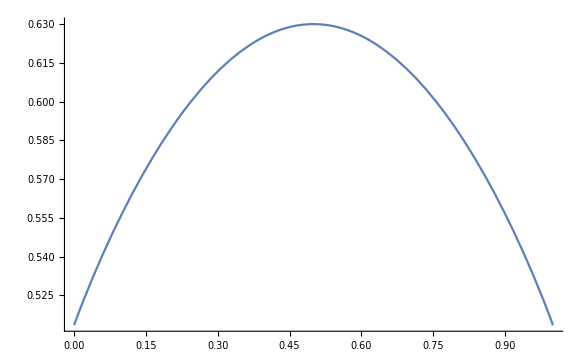

```mathematica
(*tbl = Table[{L,DetCT2[25,L,Numeric->True]},{L,1,24}];
ListPlot[tbl]*)

f[x_,y_]:=x^(-1/12)*y^(-1/12)*x^((1/y-x)/6-1/3)*y^((1/x-y)/6-1/3);
Plot[f[x,1-x]^4*x(1-x), {x,0,1}]
```

```mathematica
MatrixForm[Chop[MatrixCT2[5,2,Numeric->False]]]

Simplify[GammaPV2[3,1,Numeric->False]]

MatrixForm[Chop[MatrixMT2[5,2,Numeric->True]]]
MatrixForm[Chop[OmegaV2[5,2,Numeric->True]]]
MatrixForm[Chop[OmegaW2[5,2,Numeric->True]]]
Chop[GammaPV2[5,2,Numeric->True]]
Chop[GammaPW2[5,2,Numeric->True]]

MatrixForm[Chop[MatrixMT2[5,3,Numeric->True]]]
MatrixForm[Chop[OmegaV2[5,3,Numeric->True]]]
MatrixForm[Chop[OmegaW2[5,3,Numeric->True]]]
Chop[GammaPV2[5,3,Numeric->True]]
Chop[GammaPW2[5,3,Numeric->True]]
```

(1 | 0 | 0 | 0 | 0
0 | -((1-ⅇ^(-(4 ⅈ π)/5)) Cos[(3 π)/20])/(√10 (1-ⅇ^(-(3 ⅈ π)/5))) | ((1-ⅇ^(-(4 ⅈ π)/5)) Cos[π/15])/(√15 (1-ⅇ^(-(4 ⅈ π)/15))) | ((1-ⅇ^(-(4 ⅈ π)/5)) Cos[(7 π)/30])/(√15 (1-ⅇ^(-(14 ⅈ π)/15))) | -(ⅇ^(-(ⅈ π)/4) (1-ⅇ^(-(4 ⅈ π)/5)) Cos[(3 π)/20])/(√6 (1-ⅇ^((2 ⅈ π)/5)))
0 | -((1-ⅇ^((2 ⅈ π)/5)) Cos[π/20])/(√10 (1-ⅇ^(-(ⅈ π)/5))) | ((1-ⅇ^((2 ⅈ π)/5)) Cos[π/30])/(√15 (1-ⅇ^((2 ⅈ π)/15))) | ((1-ⅇ^((2 ⅈ π)/5)) Cos[(2 π)/15])/(√15 (1-ⅇ^(-(8 ⅈ π)/15))) | -(ⅇ^(-(ⅈ π)/4) (1-ⅇ^((2 ⅈ π)/5)) Cos[π/20])/(√6 (1-ⅇ^((4 ⅈ π)/5)))
0 | -((1-ⅇ^(-(2 ⅈ π)/5)) Cos[π/20])/(√10 (1-ⅇ^((ⅈ π)/5))) | ((1-ⅇ^(-(2 ⅈ π)/5)) Cos[(2 π)/15])/(√15 (1-ⅇ^((8 ⅈ π)/15))) | ((1-ⅇ^(-(2 ⅈ π)/5)) Cos[π/30])/(√15 (1-ⅇ^(-(2 ⅈ π)/15))) | -(ⅇ^(-(ⅈ π)/4) (1-ⅇ^(-(2 ⅈ π)/5)) Cos[π/20])/(√6 (1-ⅇ^(-(4 ⅈ π)/5)))
0 | -((1-ⅇ^((4 ⅈ π)/5)) Cos[(3 π)/20])/(√10 (1-ⅇ^((3 ⅈ π)/5))) | ((1-ⅇ^((4 ⅈ π)/5)) Cos[(7 π)/30])/(√15 (1-ⅇ^((14 ⅈ π)/15))) | ((1-ⅇ^((4 ⅈ π)/5)) Cos[π/15])/(√15 (1-ⅇ^((4 ⅈ π)/15))) | -(ⅇ^(-(ⅈ π)/4) (1-ⅇ^((4 ⅈ π)/5)) Cos[(3 π)/20])/(√6 (1-ⅇ^(-(2 ⅈ π)/5))))

2 (-3+√3)

(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0180699+0.0104327 ⅈ | -0.0180699+0.0104327 ⅈ | 0.212966-0.212966 ⅈ
0 | -0.0180699-0.0104327 ⅈ | 0 | 0.0334243 | -0.249741+0.066918 ⅈ
0 | 0.0180699-0.0104327 ⅈ | -0.0334243 | 0 | -0.066918+0.249741 ⅈ
0 | -0.212966+0.212966 ⅈ | 0.249741-0.066918 ⅈ | 0.066918-0.249741 ⅈ | 0)

(0 | 0.00853869-0.00853869 ⅈ | -0.986931+0.526654 ⅈ | -0.526654+0.986931 ⅈ | -0.558438
-0.00853869+0.00853869 ⅈ | 0 | -0.0868309+0.2911 ⅈ | 0.0868309+0.2911 ⅈ | -0.090133+0.090133 ⅈ
0.986931-0.526654 ⅈ | 0.0868309-0.2911 ⅈ | 0 | 0.29991 | -1.94066+1.12044 ⅈ
0.526654-0.986931 ⅈ | -0.0868309-0.2911 ⅈ | -0.29991 | 0 | -1.12044+1.94066 ⅈ
0.558438 | 0.090133-0.090133 ⅈ | 1.94066-1.12044 ⅈ | 1.12044-1.94066 ⅈ | 0)

(0 | -1.1095+1.1095 ⅈ | -0.978392+0.558521 ⅈ | -0.558521+0.978392 ⅈ | -0.0822311
1.1095-1.1095 ⅈ | 0 | -0.093868-0.2911 ⅈ | 0.093868-0.2911 ⅈ | 0.090133-0.090133 ⅈ
0.978392-0.558521 ⅈ | 0.093868+0.2911 ⅈ | 0 | -0.29991 | 0.357363+0.462856 ⅈ
0.558521-0.978392 ⅈ | -0.093868+0.2911 ⅈ | 0.29991 | 0 | -0.462856-0.357363 ⅈ
0.0822311 | -0.090133+0.090133 ⅈ | -0.357363-0.462856 ⅈ | 0.462856+0.357363 ⅈ | 0)

-4.86158

-12.1514

(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0334243 | -0.0180699-0.0104327 ⅈ | 0.249741-0.066918 ⅈ
0 | -0.0334243 | 0 | 0.0180699-0.0104327 ⅈ | 0.066918-0.249741 ⅈ
0 | 0.0180699+0.0104327 ⅈ | -0.0180699+0.0104327 ⅈ | 0 | -0.212966+0.212966 ⅈ
0 | -0.249741+0.066918 ⅈ | -0.066918+0.249741 ⅈ | 0.212966-0.212966 ⅈ | 0)

(0 | 0.00853869+0.0318668 ⅈ | -0.0318668-0.00853869 ⅈ | -1.11803+1.11803 ⅈ | -0.476207
-0.00853869-0.0318668 ⅈ | 0 | -0.0208938 | -0.330152+0.387525 ⅈ | -0.135199+0.0780574 ⅈ
0.0318668+0.00853869 ⅈ | 0.0208938 | 0 | 0.330152+0.387525 ⅈ | -0.0780574+0.135199 ⅈ
1.11803-1.11803 ⅈ | 0.330152-0.387525 ⅈ | -0.330152-0.387525 ⅈ | 0 | -2.30993+2.30993 ⅈ
0.476207 | 0.135199-0.0780574 ⅈ | 0.0780574-0.135199 ⅈ | 2.30993-2.30993 ⅈ | 0)

(0 | -0.978392+0.558521 ⅈ | -0.558521+0.978392 ⅈ | -1.1095+1.1095 ⅈ | 0.0822311
0.978392-0.558521 ⅈ | 0 | -0.29991 | 0.093868+0.2911 ⅈ | -0.357363-0.462856 ⅈ
0.558521-0.978392 ⅈ | 0.29991 | 0 | -0.093868+0.2911 ⅈ | 0.462856+0.357363 ⅈ
1.1095-1.1095 ⅈ | -0.093868-0.2911 ⅈ | 0.093868-0.2911 ⅈ | 0 | -0.090133+0.090133 ⅈ
-0.0822311 | 0.357363+0.462856 ⅈ | -0.462856-0.357363 ⅈ | 0.090133-0.090133 ⅈ | 0)

-3.83354

-12.1514

```mathematica
Simplify[Abs[-(((1-E^(-((4 I π)/5))) Cos[(3 π)/20])/(Sqrt[10] (1-E^(-((3 I π)/5)))))]]
Simplify[Arg[-(((1-E^(-((4 I π)/5))) Cos[(3 π)/20])/(Sqrt[10] (1-E^(-((3 I π)/5)))))]]

ClearAll[RationalizeDe];
RationalizeDe[c_,M_]:=Module[{a,b,cc,bbar},
cc=c/.{Pi->α/M};
a=Numerator[cc];
b=Denominator[cc];
bbar = Simplify[Conjugate[b],Assumptions->{α∈Reals}];
a = TrigFactor[ExpToTrig[ComplexExpand[a*bbar]]];
b=TrigFactor[ExpToTrig[ComplexExpand[b * bbar]]];
(*Print["a=",a," b=",b];*)
(*a=Simplify[Re[a]/b]+I*FullSimplify[Im[a]/b];*)
Return[Simplify[TrigReduce[a/b]]]
];

RationalizeDe[-(((1-E^(-((4 I π)/5))) Cos[(3 π)/20])/(Sqrt[10] (1-E^(-((3 I π)/5))))),5]
RationalizeDe[((1-E^(-((4 I π)/5))) Cos[π/15])/(Sqrt[15] (1-E^(-((4 I π)/15)))),5]
```

Cos[(3 π)/20]/(√(5+√5))

π+ArcTan[(4 (-(5+√5)^(3/2)/(8 √2)+Im[ⅇ^(-(4 ⅈ π)/5)] (-1+Re[ⅇ^(-(3 ⅈ π)/5)])))/(5+3 √5)]

-(√(2/5) Cos[α/100] (Cos[α/50]+Cos[(3 α)/50]) (Cos[α/50]-ⅈ Sin[α/50]))/(1+2 Cos[α/50])

((Cos[α/75]+Cos[α/25]+Cos[α/15]) (Cos[(4 α)/75]-ⅈ Sin[(4 α)/75]))/(√15)